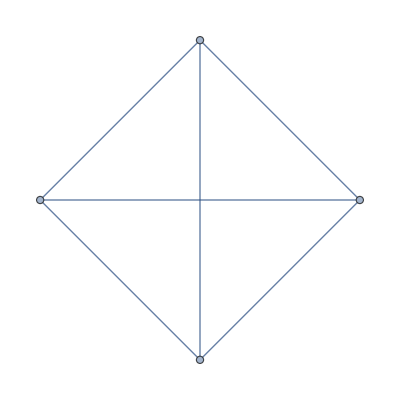

```mathematica
gg=EdgeContract[CompleteGraph[5],1<->2]
```

```mathematica
ChromaticPolynomial[gg,4]
```

24

```mathematica
ChromaticPolynomial[EdgeDelete[CompleteGraph[5],1<->2],4]
```

24

```mathematica
Table[ShowGraph5Least[k],{k,Sort[allGraphs5AtomKeys,allGraphs5[#1,"colofour"]<allGraphs5[#2,"colofour"]&]}]
```

{-Graphics-295240,-Graphics-295250,-Graphics-295270,-Graphics-295330,-Graphics-295371,-Graphics-295510,-Graphics-295600,-Graphics-296050,-Graphics-296080,-Graphics-296330,-Graphics-297670,-Graphics-297681,-Graphics-297970,-Graphics-298571,-Graphics-298881,-Graphics-302530,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-305861,-Graphics-317110,-Graphics-317140,-Graphics-317380,-Graphics-319540,-Graphics-319840,-Graphics-324411,-Graphics-326841,-Graphics-360850,-Graphics-360860,-Graphics-361120,-Graphics-361660,-Graphics-361940,-Graphics-368170,-Graphics-368980,-Graphics-382810,-Graphics-383080,-Graphics-390141,-Graphics-492070,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-492201,-Graphics-499631,-Graphics-499721,-Graphics-514750,-Graphics-514780,-Graphics-522321,-Graphics-560111,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
allGraphs5[27229,"parents"]
```

{27228,27226,27220,26986,26500,20668,7546}

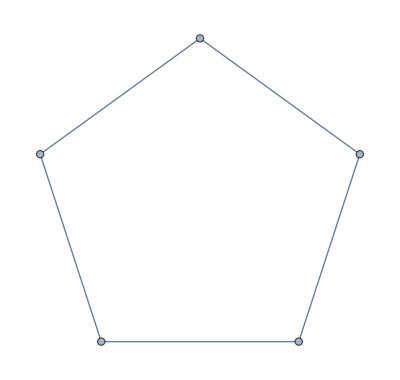

```mathematica
CycleGraph[5]
```

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},Fold[And,Table[EdgeQ[g,e],{e,EdgeList[CycleGraph[5]]}]]&&IsomorphicGraphQ[g,allGraphs5[27226,"graph"]]]&]
```

{27226,22852,20746,20692,20668}

```mathematica
Table[ShowGraph5Least[k]<->allGraphs5[k,"colofour"]/.RepGraph["C"],{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},Fold[And,Table[EdgeQ[g,e],{e,EdgeList[CycleGraph[5]]}]]&&IsomorphicGraphQ[g,allGraphs5[27226,"graph"]]]&]}]//TableForm
```

-Graphics-272262<->-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240
-Graphics-228522<->-Graphics-361660+-Graphics-361120+-Graphics-296080+-Graphics-360850+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240
-Graphics-207462<->-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-360850+-Graphics-317110+-Graphics-295510+-Graphics-295270+-Graphics-295240
-Graphics-206922<->-Graphics-361660+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295270+-Graphics-295240
-Graphics-206682<->-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240

```mathematica
Table[ShowGraph5Least[k]<->allGraphs5[k,"colofour"]/.RepGraph["C"],{k,{27228,27226,27220,26986,26500,20668,7546}}]//TableForm
```

-Graphics-272282<->-Graphics-296330+-Graphics-317380+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295250+-Graphics-295240
-Graphics-272262<->-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240
-Graphics-272202<->-Graphics-317380+-Graphics-295600+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-295510+-Graphics-295240
-Graphics-269862<->-Graphics-319540+-Graphics-317380+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240
-Graphics-265002<->-Graphics-303340+-Graphics-317380+-Graphics-317110+-Graphics-296050+-Graphics-302530+-Graphics-295510+-Graphics-295240
-Graphics-206682<->-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240
-Graphics-75462<->-Graphics-514750+-Graphics-317380+-Graphics-492070+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240

```mathematica
Table[ShowGraph5Least[k]<->allGraphs5[k,"colofour"]/.RepGraph["C"],{k,Join[amigos,alfas]}]//TableForm
```

-Graphics-294131<->-Graphics-296080+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240
-Graphics-207731<->-Graphics-317140+-Graphics-360850+-Graphics-317110+-Graphics-295270+-Graphics-295240
-Graphics-272291<->-Graphics-317380+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295240
-Graphics-229331<->-Graphics-361120+-Graphics-360850+-Graphics-295510+-Graphics-295270+-Graphics-295240
-Graphics-206951<->-Graphics-361660+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295240
-Graphics-359771<->-Graphics-361660+-Graphics-361120+-Graphics-360850
-Graphics-316811<->-Graphics-317380+-Graphics-317140+-Graphics-317110
-Graphics-230411<->-Graphics-361660+-Graphics-296080+-Graphics-296050
-Graphics-208031<->-Graphics-361120+-Graphics-317380+-Graphics-295510
-Graphics-272591<->-Graphics-317140+-Graphics-296080+-Graphics-295270

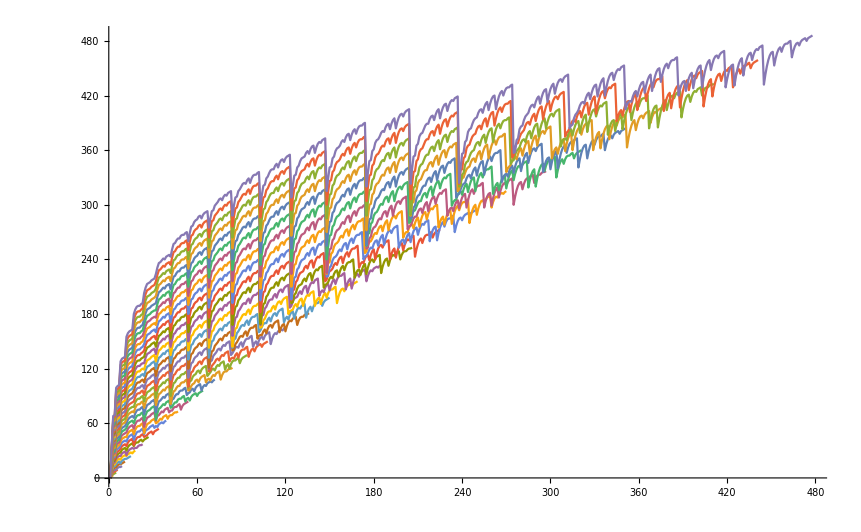

```mathematica
Monitor[ListLinePlot[Table[Map[EdgeCount[#]-(3k-6)&,BarelyNColorableGraphsOfCount[k,4]],{k,6,40}]],k]
```

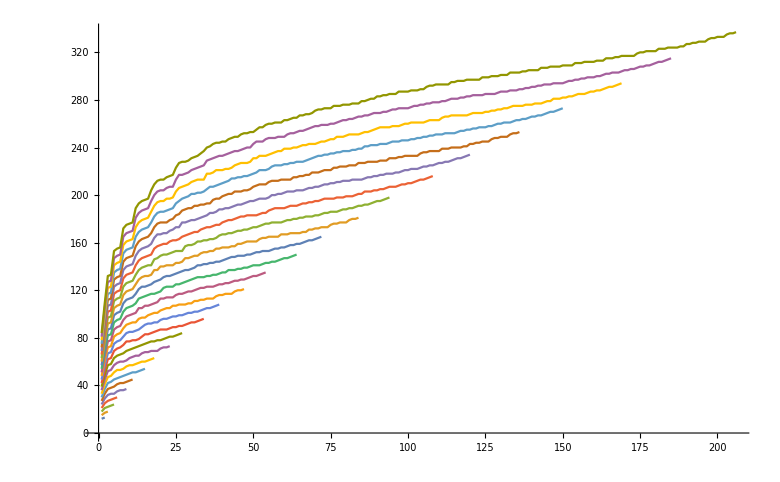

```mathematica
Monitor[ListLinePlot[Table[Sort[Map[EdgeCount[#]&,BarelyNColorableGraphsOfCount[k,4]]],{k,6,30}]],k]
```